## Scattering Rates, for electrons, and for phonons;

#### Get scattering Rates;

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/EPW/ZrC/LDA/"];
temps={"0K","10K","300K","500K","760K","1000K","1500K","1900K","2500K","3200K","3800K"};
scatteringRatesE=Table[ReadList[StringJoin["Variable_Volume/ScatteringRates/constant_smearing/kRandom/",ToString@temps[[i]],"/scattering_rate",ToString@temps[[i]]],{Number, Number,Number, Number,Number}],{i,1,11}];
```

#### Parse rates and lives;

```mathematica
(*To convert meV to THz, multiply by 3.0385309*10^12*)
```

```mathematica
scatteringRatesE300=ReadList["/Volumes/MicroSD/Dropbox/EPW/ZrC/LDA/Variable_Volume/ScatteringRates/constant_smearing/kRandom/300K/scattering_rate300K",{Number, Number,Number, Number,Number}];
```

```mathematica
scatteringRatesPh300=ReadList["/Volumes/MicroSD/Dropbox/EPW/ZrC/LDA/Variable_Volume/ScatteringRates/constant_smearing/kRandom/300K/ph_scattering_rate_meV_to_ph300K",{Number, Number,Number, Number,Number,Number}];
```

```mathematica
scatteringRatesPh3800=ReadList["/Volumes/MicroSD/Dropbox/EPW/ZrC/LDA/Variable_Volume/ScatteringRates/constant_smearing/kRandom/3800K/ph_scattering_rate_meV_to_ph3800K",{Number, Number,Number, Number,Number,Number}];
```

```mathematica
scatteringRatesE3800=ReadList["/Volumes/MicroSD/Dropbox/EPW/ZrC/LDA/Variable_Volume/ScatteringRates/constant_smearing/kRandom/3800K/scattering_rate3800K",{Number, Number,Number, Number,Number}];
```

```mathematica
rateData300E=Transpose[{Transpose[scatteringRatesE300][[3]],(10^-12)*Transpose[scatteringRatesE300][[4]]}];
```

```mathematica
rateData3800E=Transpose[{Transpose[scatteringRatesE3800][[3]],(10^-12)*Transpose[scatteringRatesE3800][[4]]}];
```

```mathematica
rateData300Ph=Transpose[{Transpose[scatteringRatesPh300][[5]],Transpose[scatteringRatesPh300][[6]]}];
```

```mathematica
rateData3800Ph=Transpose[{Transpose[scatteringRatesPh3800][[5]],Transpose[scatteringRatesPh3800][[6]]}];
```

```mathematica
rateData300E[[1]]
```

{-1.37236,198.29}

```mathematica
rateData300Ph[[1]]
```

{6.67428,0.000946422}

```mathematica
rateData300E5=RandomSample[rateData300E,10^5];
```

```mathematica
rateData3800E5=RandomSample[rateData3800E,10^5];
```

```mathematica
rateData300Ph5=RandomSample[rateData300Ph,10^5];
```

```mathematica
rateData3800Ph5=RandomSample[rateData3800Ph,10^5];
```

```mathematica
(*Electron self-energy from electron-phonon coupling*)
```

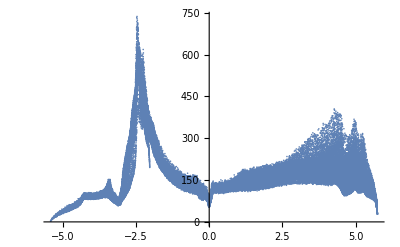

```mathematica
ListPlot@rateData300E5
```

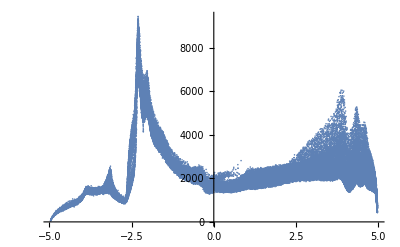

```mathematica
ListPlot@rateData3800E5
```

```mathematica
(*Phonon self-energy from electron-phonon coupling*)
```

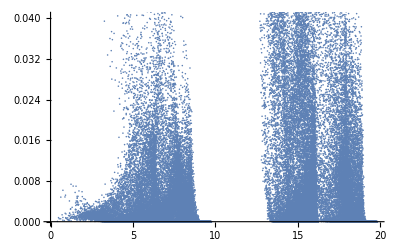

```mathematica
ListPlot@rateData300Ph5
```

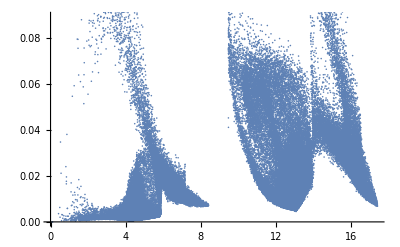

```mathematica
ListPlot@rateData3800Ph5
```